{1+1/8 (1-√17),1/4 (-1+√17)}

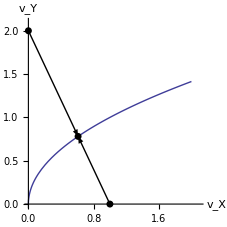

```mathematica
{x,y}={1-r,2r}/.Solve[1-r==k2/k1(2r)^2/.{k1->1,k2->1},r]⟦2⟧
g=Plot[√vx,{vx,0,2}];
Show[g,Graphics[
{
AbsolutePointSize[5],
Arrow[{{1,0},{x,y}}],Arrow[{{0,2},{x,y}}],
Point[{1,0}],Point[{0,2}],Point[{x,y}]
}
],Axes->True,PlotRange->{{0,2.1},{0,2.1}},AxesLabel->{"v_X","v_Y"},AspectRatio->1]
```